## Isaac Lewis Mathematica Mini-Project: Branched Chained Radioactive Decay

```mathematica
Quit
```

```mathematica
symsol=DSolve[
{A'[t]==-kAB*A[t]-kAC*A[t],
B'[t]==kAB*A[t]-kBD*B[t],
W'[t]==kAC*A[t]-kCD*W[t],
T'[t]==kBD*B[t]+kCD*W[t],
A[0]==A0,B[0]==0,W[0]==0,T[0]==0},
{A[t],B[t],W[t],T[t]},t
]
```

{{A[t]→A0 ⅇ^((-kAB-kAC) t),B[t]→-(A0 ⅇ^(-kBD t) (-1+ⅇ^((-kAB-kAC) t+kBD t)) kAB)/(kAB+kAC-kBD),T[t]→-1/((-kAB-kAC+kBD) (kAB+kAC-kCD))A0 ⅇ^(-kBD t-kCD t) (-ⅇ^(kCD t) kAB^2+ⅇ^(kBD t+kCD t) kAB^2-ⅇ^(kBD t) kAB kAC-ⅇ^(kCD t) kAB kAC+2 ⅇ^(kBD t+kCD t) kAB kAC-ⅇ^(kBD t) kAC^2+ⅇ^(kBD t+kCD t) kAC^2-ⅇ^(kBD t+kCD t) kAB kBD+ⅇ^((-kAB-kAC) t+kBD t+kCD t) kAB kBD+ⅇ^(kBD t) kAC kBD-ⅇ^(kBD t+kCD t) kAC kBD+ⅇ^(kCD t) kAB kCD-ⅇ^(kBD t+kCD t) kAB kCD-ⅇ^(kBD t+kCD t) kAC kCD+ⅇ^((-kAB-kAC) t+kBD t+kCD t) kAC kCD+ⅇ^(kBD t+kCD t) kBD kCD-ⅇ^((-kAB-kAC) t+kBD t+kCD t) kBD kCD),W[t]→(A0 ⅇ^(-kCD t) (-1+ⅇ^((-kAB-kAC) t+kCD t)) kAC)/(-kAB-kAC+kCD)}}

Above we have a symbolic representation of the problem in 11.14 of branched chained radioactive decay. I had to switch C[t] and D[t] with W[t] and T[t] respectively due to C and D being protected. Output provides equation to solve for decay for A[t], B[t], W[t], and  T[t] to match what we see in diagram for problem 11.14 pg 341 CPSUP book.

```mathematica
params={kAB->0.1,kAC->0.1,kBD->0.1,kCD->0.5,A0->100};
numSol =NDSolve[{A'[t]==-kAB*A[t]-kAC*A[t],B'[t]==kAB*A[t]-kBD*B[t],W'[t]==kAC*A[t]-kCD*W[t],T'[t]==kBD*B[t]+kCD*W[t],A[0]==A0,B[0]==0,W[0]==0,T[0]==0}/. params,{A,B,W,T},{t,0,50}];
```

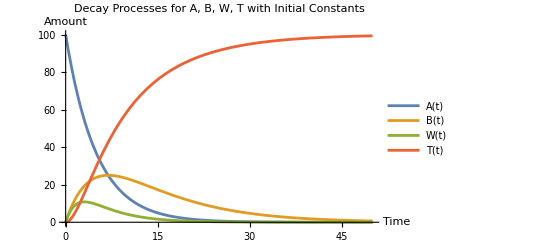

```mathematica
Plot[Evaluate[{A[t],B[t],W[t],T[t]}/. numSol],{t,0,50},PlotLegends->{"A(t)","B(t)","W(t)","T(t)"},AxesLabel->{"Time","Amount"},PlotLabel->"Decay Processes for A, B, W, T with Initial Constants"]
```

This plot represents the result with  kAB = .1, kAC =.1, kBD = .1, and kCD = .5  and shows the decay through time. The graph makes sense because A(t) continually decreases while B(t) and W(t) increase then decrease as they decay into T(t). Remember that C(t) = W(t) and D(t) = T(t). I had to do this because of mathematica’s protected variables.

In this next graph kBD = .05 and kCD = .75

```mathematica
paramstwo={kAB->0.1,kAC->0.1,kBD->0.05,kCD->0.75,A0->100};
numSol =NDSolve[{A'[t]==-kAB*A[t]-kAC*A[t],B'[t]==kAB*A[t]-kBD*B[t],W'[t]==kAC*A[t]-kCD*W[t],T'[t]==kBD*B[t]+kCD*W[t],A[0]==A0,B[0]==0,W[0]==0,T[0]==0}/. paramstwo,{A,B,W,T},{t,0,50}];
```

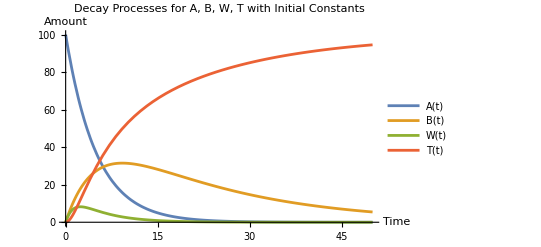

```mathematica
Plot[Evaluate[{A[t],B[t],W[t],T[t]}/. numSol],{t,0,50},PlotLegends->{"A(t)","B(t)","W(t)","T(t)"},AxesLabel->{"Time","Amount"},PlotLabel->"Decay Processes for A, B, W, T with Initial Constants"]
```

We  can  see  the  difference  in  the  decay  of  B (t)  when kBD = 0.05 and kCD = 0.75 as it takes longer for it to decay completely and also we can see the difference in the curve that represents the decay of T(t) when as the curve is flatter which shows it is taking longer for it to increase.

```mathematica
Clear[A,B,W,T,t]
```

Below, we  are  solving  the  problem  numerically  for  the  parameters  kAB = 0.1, kAC = 0.1, kBD = 0.1, kCD = 0.5, A0 = 100

```mathematica
paramstwo={kAB->0.1,kAC->0.1,kBD->0.1,kCD->0.5,A0->100};
numSol =NDSolve[{A'[t]==-kAB*A[t]-kAC*A[t],B'[t]==kAB*A[t]-kBD*B[t],W'[t]==kAC*A[t]-kCD*W[t],T'[t]==kBD*B[t]+kCD*W[t],A[0]==A0,B[0]==0,W[0]==0,T[0]==0}/. paramstwo,{A,B,W,T},{t,0,50}]
```

{{A→InterpolatingFunction[…],B→InterpolatingFunction[…],W→InterpolatingFunction[…],T→InterpolatingFunction[…]}}

```mathematica
Clear[A,B,W,T,t]
```

Below, we   are   solving   the   problem   numerically   for   the   parameters   kAB = 0.1, kAC = 0.1, kBD = 0.05, kCD = 0.75, A0 = 100

```mathematica
paramstwo={kAB->0.1,kAC->0.1,kBD->0.05,kCD->0.75,A0->100};
numSol =NDSolve[{A'[t]==-kAB*A[t]-kAC*A[t],B'[t]==kAB*A[t]-kBD*B[t],W'[t]==kAC*A[t]-kCD*W[t],T'[t]==kBD*B[t]+kCD*W[t],A[0]==A0,B[0]==0,W[0]==0,T[0]==0}/. paramstwo,{A,B,W,T},{t,0,50}]
```

{{A→InterpolatingFunction[…],B→InterpolatingFunction[…],W→InterpolatingFunction[…],T→InterpolatingFunction[…]}}

```mathematica
Clear[A,B,W,T,t]
```

```mathematica
Manipulate[Module[{sol,A,B,W,T,t},sol=NDSolve[{A'[t]==-kAB*A[t]-kAC*A[t],B'[t]==kAB*A[t]-kBD*B[t],W'[t]==kAC*A[t]-kCD*W[t],T'[t]==kBD*B[t]+kCD*W[t],A[0]==100,B[0]==0,W[0]==0,T[0]==0},{A,B,W,T},{t,0,50}];
Plot[Evaluate[{A[t],B[t],W[t],T[t]}/. sol],{t,0,50},PlotLegends->{"A(t)","B(t)","W(t)","T(t)"},AxesLabel->{"Time","Amount"},PlotRange->All,PlotLabel->"Decay Processes for A, B, W, T with Varying Constants"]],{{kAB,0.1,"Decay Rate kAB"},0,1,0.01},{{kAC,0.1,"Decay Rate kAC"},0,1,0.01},{{kBD,0.1,"Decay Rate kBD"},0,1,0.01},{{kCD,0.5,"Decay Rate kCD"},0,1,0.01},TrackedSymbols->{kAB,kAC,kBD,kCD},ControlPlacement->Left]
```

Above  we  have  an  animated  graph for decay with controls for kAB, kAC, kBD, kCD

```mathematica
Clear[A,B,W,T,t]
```